# LD Power Curves

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Moglabs 780 nm “780B”

7/17/19-7/18/19

```mathematica
powerNoFilter = {0.018,0.044,0.079,0.149,4,12.24,17.49,23.72,28.5,31.84};
current100 = {10,20,30,40,50,60,70,80,90,100};
```

```mathematica
powerFilter = {0.001,0.00195,0.0034,0.0057,1.8,7.84,12.85,18.26,21.75,24.28,25.85,25.88,26.45,26.38,25.77};
current150 = {10,20,30,40,50,60,70,80,90,100,110,120,130,140,150};
```

```mathematica
powerBareDiode = {0.005,0.014,0.023,0.035,0.052,0.078,0.120,0.188,0.294,0.449,0.670,0.98,1.41,1.976,2.693};
```

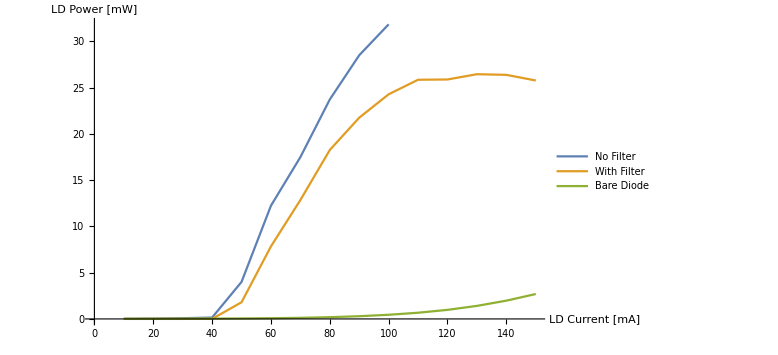

```mathematica
ListPlot[{Transpose@{current100,powerNoFilter},Transpose@{current150,powerFilter},Transpose@{current150,powerBareDiode}},Joined->True,AxesLabel->{"LD Current [mA]","LD Power [mW]"},PlotLegends->{"No Filter","With Filter","Bare Diode"},ImageSize->Large]
```

7/18/19

```mathematica
WignerD[{2,0,0},5.6*π/180]
```

0.985716

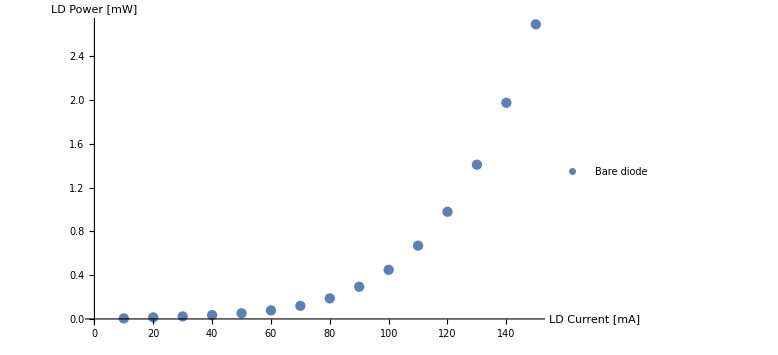

```mathematica
ListPlot[{Transpose@{current150,powerBareDiode}},AxesLabel->{"LD Current [mA]","LD Power [mW]"},PlotLegends->{"Bare diode"},ImageSize->Large]
```

```mathematica
Moglabs 780 nm "780B"
```

## Homemade ECDL “780A”

2019/09/05

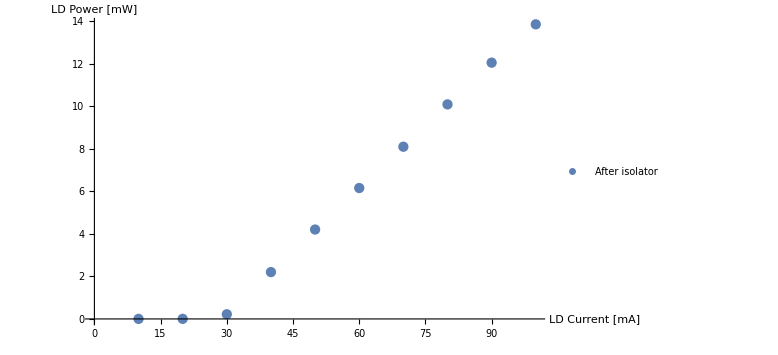

```mathematica
current = Table[10i,{i,1,10}]; (*mA*)
power = {0.0019,0.0045,0.220,2.2,4.2,6.15,8.09,10.08,12.04,13.84}; (*mW, after isolators*)
ListPlot[{Transpose@{current,power}},AxesLabel->{"LD Current [mA]","LD Power [mW]"},PlotLegends->{"After isolator"},ImageSize->Large]
```

## 480 SHG

I2V

```mathematica
mV = {21.6,10.4,35.2,47.2,66.4,83.2,105};
mW = {2.74,1.3,4.51,6.08,8.52,10.72,13.67}*1.06;
```

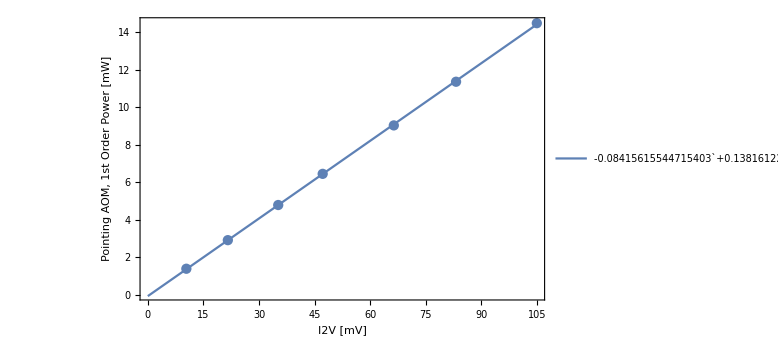

```mathematica
plt=Show[ListPlot[{Transpose@{mV,mW}},AxesLabel->{"LD Current [mA]","LD Power [mW]"},ImageSize->Large,Axes->False,Frame->{True,True,False,False},FrameLabel->{"I2V [mV]","Pointing AOM, 1st Order Power [mW]"},LabelStyle->Directive[Black, FontFamily-> "Times",FontSize->20]],Plot[-0.08415615544715403+0.13816122788111132 x,{x,0,105},PlotLegends->{"-0.08415615544715403`+0.13816122788111132` x"}]]
```

```mathematica
Export["480_i2v_power_curve.png",plt,ImageResolution-> 100]
```

480_i2v_power_curve.png

```mathematica
Fit[Transpose@{mV,mW},{1,x},x]
```

-0.0841562+0.138161 x

```mathematica
Plot[]
```